```mathematica
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","Polynomial","TestSuite"}]];
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];
$MaxExtraPrecision=1000;
(*Worland package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Worland`$mpprec=100;
Worland`$WorlandType="SphEnergy";
Needs["Worland`"]
ParallelNeeds["Worland`"]
datadir={"_data","Polynomial","Worland",$WorlandType};
refdir={"_refdata","Polynomial","Worland",$WorlandType};

dealiasGrid[n_,l_]:=Floor[3(n+l/2+8)/2];
(*
Configure which output to generate
*)
genRefDataDefault=False;
generateRefData=genRefDataDefault;
configureGenerator[genRef_:genRefDataDefault]:=
Module[{},
generateRefData=genRef;
];
(*
Metadata format
*)
createMetadata[nN_, gridN_,l_]:=Module[{descr,header },
header={
"# Format description",
"# line 1: number of lines",
"# line 2: radial modes", 
"# line 3: radial grid points", 
"# line 4: harmonic degree l" 
};
descr = Flatten[{nN,gridN,l}];
descr = Prepend[descr,Length@descr];
descr = Flatten[Prepend[descr,header]];
descr
];
```

```mathematica
(*Check basic setup*)
(*ng=20;
rg = wgrid[ng];
wg=wweights[ng];
Table[N[Table[Dot[Wnl[i,l,rg],wg Wnl[j,l,rg]],{i,0,5},{j,0,5}],5]//MatrixForm,{l,0,5}]
Clear[ng, rg, wg]*)
```

```mathematica
refop[ns_,gfunc_,wfunc_,opfunc_,name_]:= Module[{outprec = 32,i,maxN,gridN,l, grid,weights, op,msg,descr,tempmsg,fname},
For[i = 1, i≤ Length[ns],i++,
maxN=ns[[i,1]];
gridN = ns[[i,2]];
l=ns[[i,3]];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[maxN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[l]<>"...";
tempmsg=PrintTemporary[msg];
(* Generate metadata *)
fname=name<>"_id"<>ToString[l]<>"_meta.dat";
descr = createMetadata[maxN,gridN,l];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
fname="weighted_"<>fname;
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate operator *)
If[generateRefData,
grid = gfunc[gridN];
weights=wfunc[gridN];
op=Transpose[Table[opfunc[n,l,grid],{n,0,maxN}]];
op = N[op,outprec];
fname=name<>"_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],op];
fname="weighted_"<>fname;
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],weights*op];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
];
]
```

```mathematica
maxN=128;
maxL=256;
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,Wnl,"Wnl"];
Clear[maxN,maxL,gridN,tests];
```

{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}}

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 0... Done(Fri 10 Jul 2026 17:54:15)

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 1... Done(Fri 10 Jul 2026 17:54:25)

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 2... Done(Fri 10 Jul 2026 17:54:35)

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 5... Done(Fri 10 Jul 2026 17:54:46)

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 20... Done(Fri 10 Jul 2026 17:54:56)

Exporting Wnl Worland operator for N = 128, Ng = 256, l = 128... Done(Fri 10 Jul 2026 17:55:06)

```mathematica
maxN=128;
maxL=256;
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,dWnl,"dWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,slaplWnl,"slaplWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_recurrence_t"];
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_explicit_t"];
configureGenerator[True];
refop[tests,wgrid,wweights,divrWnl,"r_1Wnl_implicit_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN=2maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,drWnl,"drWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
ddivrWnl[1,1,r]
```

ddivrWnl[1,1,r]

```mathematica
maxN=128;
maxL=256;
gridN=2maxN;
tests=Table[{maxN,gridN,l},{l,{1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,ddivrWnl,"dr_1Wnl"];
Clear[maxN,maxL,gridN,tests];
```

{{128,256,0},{128,256,1},{128,256,2},{128,256,5},{128,256,20},{128,256,128}}

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 0... Done(Fri 10 Jul 2026 18:25:21)

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 1... Done(Fri 10 Jul 2026 18:25:35)

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 2... Done(Fri 10 Jul 2026 18:25:50)

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 5... Done(Fri 10 Jul 2026 18:26:04)

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 20... Done(Fri 10 Jul 2026 18:26:19)

Exporting dr_1Wnl Worland operator for N = 128, Ng = 256, l = 128... Done(Fri 10 Jul 2026 18:26:33)

```mathematica
maxN=128;
maxL=256;
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
refop[tests,wgrid,wweights,divrdrWnl,"r_1drWnl_recurrence_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
refop[tests,wgrid,wweights,ddivrdrWnl,"dr_1drWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2 maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
refop[tests,wgrid,wweights,claplhWnl,"claplhWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2maxN;
configureGenerator[True];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
refop[tests,wgrid,wweights,dclaplhWnl,"dclaplhWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN = 2 maxN;
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refop[tests,wgrid,wweights,divrclaplhWnl,"r_1claplhWnl"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
refDenseOp[ns_,gfunc_,wfunc_,opfunc_,name_]:= Module[{outprec = 32,i,maxN,gridN,l, grid,weights, op,msg,descr,tempmsg,fbase,fname},
For[i = 1, i≤ Length[ns],i++,
maxN=ns[[i,1]];
gridN = ns[[i,2]];
l=ns[[i,3]];
fbase="weighted_"<>name;
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[maxN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[l]<>"...";
tempmsg=PrintTemporary[msg];
(* Generate metadata *)
fname=fbase<>"_id"<>ToString[l]<>"_meta.dat";
descr = createMetadata[maxN,gridN,l];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate operator *)
If[generateRefData,
grid = gfunc[gridN];
weights=wfunc[gridN];
op = opfunc[maxN,l,grid,weights];
op = N[op,outprec];
fname=fbase<>"_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],op];
NotebookDelete[tempmsg];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
];
]
```

```mathematica
maxN=128;
maxL=256;
configureGenerator[True];
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
refDenseOp[tests,wgrid,wweights,divrdrWnlExplicit,"r_1drWnl_explicit_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
maxN=128;
maxL=256;
gridN= dealiasGrid[maxN,maxL];
tests=Table[{maxN,gridN,l},{l,{0,1,2,5,20,128}}]
configureGenerator[True];
refDenseOp[tests,wgrid,wweights,divrdrWnlImplicit,"r_1drWnl_implicit_t"];
Clear[maxN,maxL,gridN,tests];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=0;
Quiet[data=ReadList[dataroot<>datadir<>"Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=110;
y=data[[;;,n+1]];
pts=Partition[Riffle[grid,y],2];
(*ref=Partition[Riffle[grid,Wnl[n,l,refgrid]],2];*)
ref=Partition[Riffle[grid,Wnl[n,l,grid]],2];
err = Partition[Riffle[grid, Abs[SetPrecision[pts[[;;,2]],$mpprec]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[SetPrecision[pts[[;;,2]],$mpprec]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,y,pts,ref,err,relerr,pl1,pl2,zoomn,grid,imax];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=0;
Quiet[data=ReadList[dataroot<>datadir<>"dWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=27;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,dWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},{Red,PointSize[Medium]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=5;
Quiet[data=ReadList[dataroot<>datadir<>"slaplWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=111;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,slaplWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
err[[1+40]]
relerr[[1+40]]
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"r_1Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,divrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

ReadList::noopen: Cannot open /Users/stefanomaffei/QuICC/QuICC_mnt/QuICC-Solver-merge/build/Components/Polynomial/TestSuite_dataPolynomialWorlandSphEnergydr_1Wnl_l1_n128_g256.dat.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«11»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

{1,0.00306496,2.65192×10^-6 Abs[{Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[]}+{377085.,901343.,914354.,513079.,50747.5,-173108.,-122979.,22654.7,84468.4,33963.9,-35886.4,-43785.,49.4892,31829.6,18528.5,-13327.,-22180.6,-2630.89,16126.3,11726.1,-6166.13,-13370.9,-2900.49,9482.92,8184.9,-3127.59,-8922.98,-2727.64,6085.91,6098.13,-1608.13,-6360.41,-2481.12,4127.87,4755.63,-764.114,-4745.28,-2244.93,2901.7,3834.51,-260.135,-3658.64,-2037.01,2085.54,3170.72,56.9046,-2890.28,-1858.14,1516.12,2673.53,264.218,-2325.19,-1704.81,1103.62,2289.31,403.812,-1896.06,-1572.92,795.398,1984.6,499.935,-1561.32,-1458.72,558.95,1737.6,567.272,-1294.16,-1359.12,373.372,1533.56,615.07,-1076.61,-1271.6,224.719,1362.19,649.346,-896.264,-1194.1,103.409,1216.08,674.127,-744.298,-1124.98,2.67943,1089.82,692.173,-614.3,-1062.9,-82.3572,979.335,705.415,-501.498,-1006.76,-155.307,881.489,715.229,-402.273,-955.629,-218.885,793.845,722.612,-313.822,-908.75,-275.175,714.461,728.3,-233.934,-865.467,-325.806,641.761,732.84,-160.833,-825.216,-372.076,574.441,736.647,-93.0596,-787.502,-415.043,511.399,740.041,-29.389,-751.879,-455.587,451.68,743.27,31.2336,-717.938,-494.46,394.436,746.532,89.7424,-685.296,-532.325,338.885,749.986,146.992,-653.577,-569.783,284.289,753.763,203.794,-622.407,-607.403,229.918,757.974,260.944,-591.395,-645.742,175.027,762.713,319.263,-560.119,-685.372,118.822,768.064,379.62,-528.11,-726.897,60.4275,774.099,442.983,-494.828,-770.989,-1.16008,780.884,510.457,-459.627,-818.415,-67.126,788.477,583.357,-421.719,-870.082,-138.915,796.922,663.285,-380.11,-927.094,-218.335,806.253,752.251,-333.519,-990.835,-307.715,816.476,852.849,-280.247,-1063.08,-410.124,827.556,968.508,-217.989,-1146.18,-529.726,839.393,1103.89,-143.528,-1243.31,-672.323,851.762,1265.52,-52.2401,-1358.92,-846.259,864.226,1462.83,62.7426,-1499.43,-1063.96,875.953,1709.97,212.025,-1674.5,-1344.7,885.366,2029.13,412.756,-1899.33,-1719.95,889.385,2457.01,694.285,-2199.27,-2244.29,881.722,3058.6,1110.6,-2619.81,-3020.29,848.554,3959.54,1770.95,-3250.86,-4262.48,755.982,5434.03,2927.86,-4296.04,-6493.71,505.562,8197.31,5294.65,-6321.82,-11333.8,-282.87,14752.8,11718.5,-11584.3,-26641.6,-4263.87,41347.7,47878.7,-41351.7,-211368.,-367729.}]}

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«11»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Abs[Symbol[]]

377084.711288495762225433653982588108276636921652101915805773901773831970976562083517198144

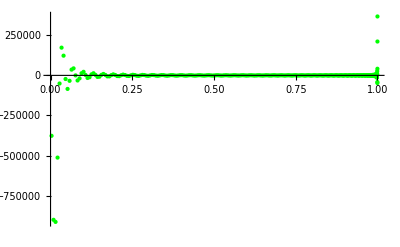

Thread::tdlen: Objects of unequal length in {Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«11»,Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],Symbol[],«205»}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"dr_1Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,ddivrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN, grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"r_1drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,divrdrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN, grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,drWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"dr_1drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,ddivrdrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"claplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,claplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"dclaplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,dclaplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"r_1claplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,divrclaplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=0;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=110;
y=data[[;;,n+1]];
pts=Partition[Riffle[grid,y],2];
(*ref=Partition[Riffle[grid,Wnl[n,l,refgrid]],2];*)
ref=Partition[Riffle[grid,weights*Wnl[n,l,grid]],2];
err = Partition[Riffle[grid, Abs[SetPrecision[pts[[;;,2]],$mpprec]-ref[[;;,2]]]],2];
relerr = Partition[Riffle[grid, Abs[SetPrecision[pts[[;;,2]],$mpprec]-ref[[;;,2]]]/Abs[ref[[;;,2]]]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Medium]},{Blue,PointSize[Small]},Blue},PlotRange->All,PlotLegends->Placed[{"Ref","QuICC"},{0.2,0.6}]],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1100,500}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,y,pts,ref,err,relerr,pl1,pl2,zoomn,grid,weights,imax];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=0;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_dWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=27;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*dWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},{Red,PointSize[Medium]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,y,grid,weights,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=5;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_slaplWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=111;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*slaplWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
err[[1+40]]
relerr[[1+40]]
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
SetPrecision[Max[Abs[pts[[1;;zoomn,2]]]],16]
N[Max[Abs[ref[[1;;zoomn,2]]]],16]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
imax = Ordering[relerr[[gridN/2;;,2]]][[-1]]+gridN/2-1;
{N[grid[[imax]],16],N[y[[imax]],16],N[relerr[[imax,2]],16]}
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=0;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_r_1Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*divrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_dr_1Wnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*ddivrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN, grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_r_1drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*divrdrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN, grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*drWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_dr_1drWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=118;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*ddivrdrWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_claplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*claplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_dclaplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*dclaplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```

```mathematica
Clear[data]
maxN=128;
gridN=256;
l=1;
Quiet[data=ReadList[dataroot<>datadir<>"weighted_r_1claplhWnl_l"<>ToString[l]<>"_n"<>ToString[maxN]<>"_g"<>ToString[gridN]<>".dat", Number, RecordLists->True],General::munfl];
grid=wgrid[gridN];
weights=wweights[gridN];
n=100;
y=SetPrecision[data[[;;,n+1]],$mpprec];
pts=Partition[Riffle[grid,y],2];
ref=Partition[Riffle[grid,weights*divrclaplhWnl[n,l,grid]],2];
err = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]],General::munfl]],2];
relerr = Partition[Riffle[grid, Quiet[Abs[pts[[;;,2]]-ref[[;;,2]]]/Abs[ref[[;;,2]]],General::munfl]],2];
zoomn=FirstPosition[relerr[[;;,2]],x_/;x<10^-8][[1]];
{zoomn,grid[[zoomn]]//N,relerr[[zoomn,2]]//N}
pl1=Quiet[ListPlot[{ref,pts},PlotStyle->{{Green,PointSize[Large]},Blue},PlotRange->All],General::munfl];
pl2=Quiet[ListLogPlot[{err,relerr},PlotStyle->{{Blue,PointSize[Medium]},{Magenta,PointSize[Medium]}}, PlotRange->{All,{10^-18,All}}],General::munfl];
Max[Abs[pts[[1;;zoomn,2]]]]
Max[Abs[ref[[1;;zoomn,2]]]]
GraphicsRow[{pl1,pl2},ImageSize->{1200,400}]
Max[relerr[[gridN/2;;,2]]]//N
Clear[n,l,maxN,gridN,grid,weights,y,pts,ref,err,relerr,pl1,pl2,zoomn];
```